```mathematica
Clear[a, ks, kc,PsiIntCurved, Theta, DTheta,Dthetakc]
(*PsiIntCurved[a_,ks_,kc_]:=(ks^2+8*kc)^0.5*(kc-(kc^2-1)^0.5)^0.5*(EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2+6*kc)-((ks^2+6*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2]-EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2+6*kc)+((ks^2+6*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2]);*)
PsiIntCurved[a_,ks_,kc_]:=(ks^2)^0.5*(kc-(kc^2-1)^0.5)^0.5*(EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2-2*kc)-((ks^2-2*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2]-EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2-2*kc)+((ks^2-2*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2])
(*Note: atot[kc_] := (kc-(kc^2-1)^0.5)^0.5; for kc<1
atot[kc_]=1 for kc>1 *)
Theta[ks_, kc_]:=2*PsiIntCurved[a, ks, kc]/.{a->1};
DTheta[ks_,kc_]:=Derivative[1,0][Theta][ks,kc];
DThetakc[kc_]:=Re[DTheta[ks,kc]]/.{ks->1000};
(*Dthetakc[kc_]:=Limit[DTheta[ks,kc],ks->Infinity]*)
```

```mathematica
(* calculate eta_tot*)
2 Sqrt[3]Integrate[1/Sqrt[1-2 kc a^2+a^4],{a,0,1}]

ConditionalExpression[2 √3 (-(ⅈ √(1-kc+√(-1+kc^2)) √((-1+kc+√(-1+kc^2))/(kc+√(-1+kc^2))) EllipticF[ⅈ ArcSinh[√(1/(-kc+√(-1+kc^2)))],(kc-√(-1+kc^2))/(kc+√(-1+kc^2))])/(√(2-2 kc))+(2 ⅈ √((√(-1+kc^2))/(-kc+√(-1+kc^2))) (-((-1+kc^2)^(1/4))/(√(-1/(√(kc+√(-1+kc^2)))))+√(-√(-1+kc^2) √(kc+√(-1+kc^2)))) EllipticF[ⅈ √(1/(-kc+√(-1+kc^2))) √(-kc+√(-1+kc^2)) ArcSinh[(√(kc+√(-1+kc^2)))/(√(-kc+√(-1+kc^2)))],(kc-√(-1+kc^2))/(kc+√(-1+kc^2))])/(√(-1+kc^2) √(1/(-kc+√(-1+kc^2))) (kc+√(-1+kc^2))^(3/4))), ]
```

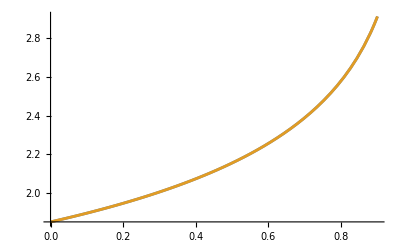

```mathematica
Clear[a,b,EtaTot, SlopeEtaTot]
a[kc_]:=kc+√(-1+kc^2);
b[kc_]:=kc-√(-1+kc^2);
EtaTot[kc_]:=2 √3 (-(ⅈ (1-b[kc]) EllipticF[ⅈ ArcSinh[√(1/(-b[kc]))],b[kc]/a[kc]])/(√(2-2 kc))+(2 ⅈ (-((-1+kc^2)^(1/4))/(√(-1/(√a[kc])))+√(-√(-1+kc^2) √a[kc])) √(1-kc a[kc]) EllipticF[ⅈ √(1/(-b[kc])) √(-b[kc]) ArcSinh[(√a[kc])/(√(-b[kc]))],b[kc]/a[kc]])/(√(-1+kc^2) √(1/(-b[kc])) (a[kc])^(3/4)));
SlopeEtaTot[kc_]:=EtaTot[kc]/Sqrt[3];
Plot[{DThetakc[kc],SlopeEtaTot[kc]},{kc,0,0.9}]
```

```mathematica
Clear[Thetakc]
Limit[Theta[ks,kc],ks->∞, Assumptions -> kc<1]
```

ConditionalExpression[(kc-(-1+kc^2)^0.5)^0.5 ∞ EllipticF[ArcSin[1/((kc-1. (-1.+kc^2)^0.5)^0.5)],(-1. kc+(-1.+kc^2)^0.5)^2], √(-1.+kc^2)∈ℝ]

```mathematica
Solve[EllipticK[1-m]==EllipticK[m],m]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

```mathematica
Solve[EllipticK[1-m]==EllipticK[m],m]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[EllipticK[1-m]==EllipticK[m],m]